```mathematica
FunctE[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
FunctE1[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]

```mathematica
FunctE2[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
GammaSMLO[omega_,gammarx_,omegarx_]=gammarx*omega/omegarx
```

(gammarx omega)/omegarx

```mathematica
MainDirecroty=NotebookDirectory[]
```

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\

```mathematica
Filename="rsf106cd_eb2005.txt";
DataExp=ReadList[FileNameJoin[{MainDirecroty,Filename}],Number];
Ncolumbs=4;
Nmaxpoints1=Length[DataExp]/Ncolumbs-1;
X1aver=Table[DataExp[[Ncolumbs*i+2]],{i,0,Nmaxpoints1}];
Y1aver=Table[DataExp[[Ncolumbs*i+3]],{i,0,Nmaxpoints1}];
dY1aver=Table[DataExp[[Ncolumbs*i+4]],{i,0,Nmaxpoints1}];
Clear[DataExp]
```

```mathematica
Needs["ErrorBarPlots`"]
```

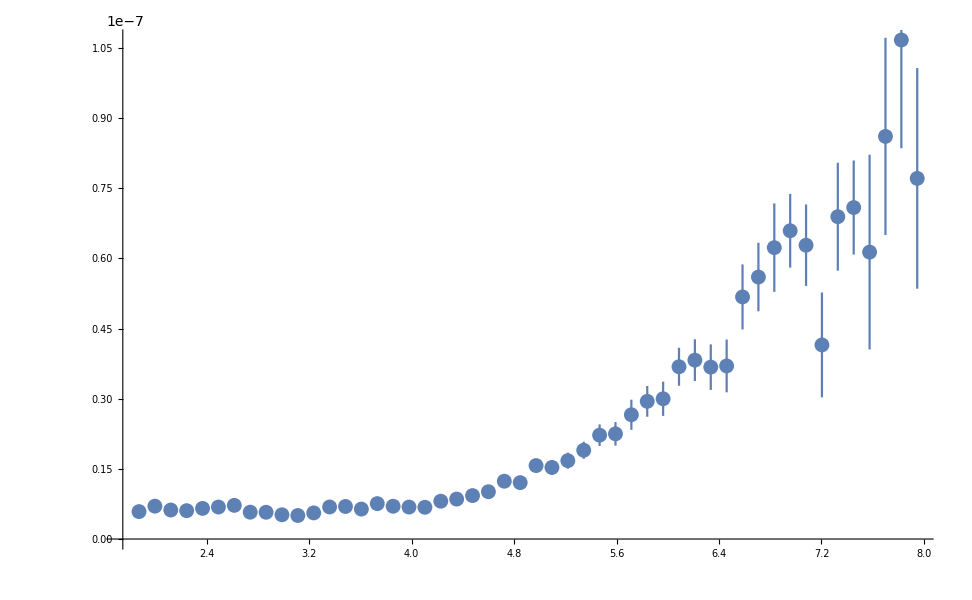

```mathematica
ErrorListPlot[{Transpose[{X1aver,Y1aver,dY1aver}]},PlotRange->All]
```

```mathematica
(* Fit  the cross section in the region [Ulow,Uupper] *)
```

```mathematica
Ulow=0.0;
Uupper=20.0;
Nlow=1;
Nupper=Length[Y1aver]
Do[If[X1aver[[i]]<Ulow,Nlow=i,Nlow=Nlow],{i,1,Length[Y1aver]}];
Do[If[X1aver[[i]]<Uupper,Nupper=i,Nupper=Nupper],{i,1,Length[Y1aver]}];
Nlow
Nupper
```

50

1

50

```mathematica
X1aver
```

{1.8715,1.9955,2.1195,2.2435,2.3675,2.4915,2.6155,2.7395,2.8635,2.9875,3.1115,3.2355,3.3595,3.4835,3.6075,3.7315,3.8555,3.9795,4.1035,4.2275,4.3515,4.4755,4.5995,4.7235,4.8475,4.9715,5.0955,5.2195,5.3435,5.4675,5.5915,5.7155,5.8395,5.9635,6.0875,6.2115,6.3355,6.4595,6.5835,6.7075,6.8315,6.9555,7.0795,7.2035,7.3275,7.4515,7.5755,7.6995,7.8235,7.9475}

```mathematica
Y1aver
```

{5.86666×10^-9,7.02504×10^-9,6.2019×10^-9,6.06183×10^-9,6.54816×10^-9,6.84132×10^-9,7.19793×10^-9,5.73946×10^-9,5.72482×10^-9,5.18361×10^-9,5.02909×10^-9,5.5857×10^-9,6.85462×10^-9,6.9606×10^-9,6.402×10^-9,7.57172×10^-9,7.01079×10^-9,6.8324×10^-9,6.78773×10^-9,8.08297×10^-9,8.54007×10^-9,9.28938×10^-9,1.01168×10^-8,1.23644×10^-8,1.20622×10^-8,1.57093×10^-8,1.53075×10^-8,1.67577×10^-8,1.89868×10^-8,2.22119×10^-8,2.24966×10^-8,2.65748×10^-8,2.94484×10^-8,2.99948×10^-8,3.68432×10^-8,3.8259×10^-8,3.6764×10^-8,3.70234×10^-8,5.17768×10^-8,5.6032×10^-8,6.23217×10^-8,6.59325×10^-8,6.28414×10^-8,4.15124×10^-8,6.89378×10^-8,7.08992×10^-8,6.13677×10^-8,8.61076×10^-8,1.06736×10^-7,7.71329×10^-8}

```mathematica
dY1aver
```

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[-Im[(2.22848×10^-7+(«1»«1»«5»)/(«1»))/(25.1854+«3»+(«19» «1»)/(«1»))+(«21»«1»«1»)/(«1»)]]

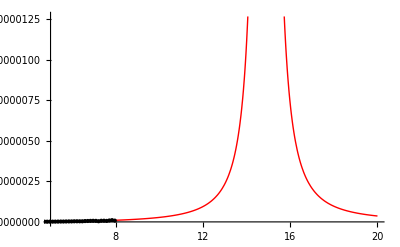

14.9075

5.01851

-0.903354

7.32068

1.05048

0.0696389

0.000472068

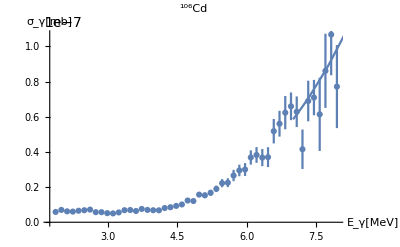

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 14.9075 | 7090.48 | 0.00210247 | 0.998332
omega2p | 5.01851 | 2456.15 | 0.00204324 | 0.998379
Gamma1p | -0.903354 | 91146.4 | -9.91102×10^-6 | 0.999992
Gamma2p | 7.32068 | 136090. | 0.0000537929 | 0.999957
Gamma12p | 1.05048 | 126895. | 8.27837×10^-6 | 0.999993
Z10 | 0.0696389 | 8474.99 | 8.21699×10^-6 | 0.999993
Z20 | 0.000472068 | 1.48051 | 0.000318855 | 0.999747

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{14.9075,7090.48,0.00210247,0.998332},{5.01851,2456.15,0.00204324,0.998379},{-0.903354,91146.4,-9.91102×10^-6,0.999992},{7.32068,136090.,0.0000537929,0.999957},{1.05048,126895.,8.27837×10^-6,0.999993},{0.0696389,8474.99,8.21699×10^-6,0.999993},{0.000472068,1.48051,0.000318855,0.999747}}

1.34652

1.34652

```mathematica
(*TSE  !!!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,Nlow,Nmaxpointstemp}];
FordY1aver=Table[dY1aver[[i]],{i,Nlow,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,10<omega1p < 15, 5<omega2p<8, 1<Gamma1p<4(*, 0<Gamma2p<2, 0<Gamma12p<1, Z10<0.01, Z20<0.01*)
},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[-Im[10.5089/(284.811+(0.+«1») «5»-omega^2)+(«20»)/(«18»+«1»-«1»)]]

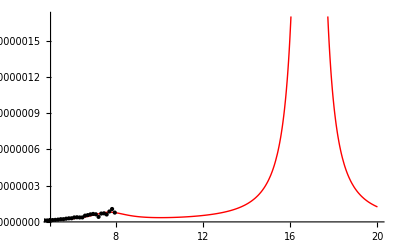

16.8763

7.75533

7.81071×10^-6

2.07607

3.24174

0.00104459

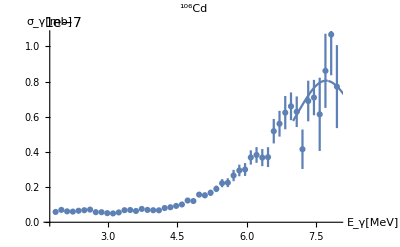

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 16.8763 | 76.3397 | 0.221069 | 0.826061
omega2p | 7.75533 | 1.04705 | 7.40684 | 2.90886×10^-9
Gamma1p | 7.81071×10^-6 | 122.868 | 6.35697×10^-8 | 1.
Gamma2p | 2.07607 | 1.99927 | 1.03842 | 0.304749
Z10 | 3.24174 | 2.54975×10^7 | 1.27139×10^-7 | 1.
Z20 | 0.00104459 | 0.00120059 | 0.870061 | 0.388989

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{16.8763,76.3397,0.221069,0.826061},{7.75533,1.04705,7.40684,2.90886×10^-9},{7.81071×10^-6,122.868,6.35697×10^-8,1.},{2.07607,1.99927,1.03842,0.304749},{3.24174,2.54975×10^7,1.27139×10^-7,1.},{0.00104459,0.00120059,0.870061,0.388989}}

8.05124

8.05124

```mathematica
(*independent Gamma12p=0 !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0, 10<omega1p < 20 },{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam0[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam0=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::eit: The algorithm does not converge to the tolerance of 1.×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.0361×10^-19,0.0158814,4.41994×10^-20}, is returned.

FittedModel[-Im[(2.287×10^-7+(«1»«1»«5»)/(«1»))/(49.1241+«3»+(«19» «1»)/(«1»))+(«23»«1»«1»)/(«1»)]]

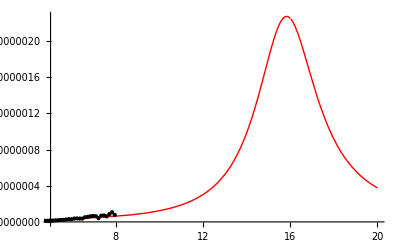

16.0153

7.00886

2.94932

1.94279

0.51674

0.0111451

0.000478226

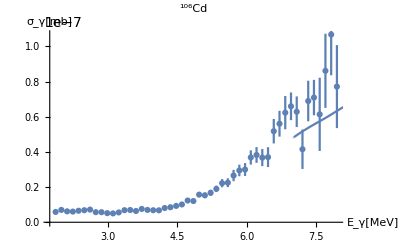

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 16.0153 | 61.9914 | 0.258347 | 0.797372
omega2p | 7.00886 | 5.62983 | 1.24495 | 0.219893
Gamma1p | 2.94932 | 61.7603 | 0.0477543 | 0.962133
Gamma2p | 1.94279 | 6.60866 | 0.293977 | 0.77019
Gamma12p | 0.51674 | 9.81072 | 0.052671 | 0.958238
Z10 | 0.0111451 | 0.0644323 | 0.172974 | 0.863484
Z20 | 0.000478226 | 0.0031228 | 0.15314 | 0.879004

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{16.0153,61.9914,0.258347,0.797372},{7.00886,5.62983,1.24495,0.219893},{2.94932,61.7603,0.0477543,0.962133},{1.94279,6.60866,0.293977,0.77019},{0.51674,9.81072,0.052671,0.958238},{0.0111451,0.0644323,0.172974,0.863484},{0.000478226,0.0031228,0.15314,0.879004}}

12.5909

12.5909

```mathematica
(*TSE SMLO GDR and PDR *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[-Im[(0.0498169+(«1»)/(«1»))/(16743.2+«1»-«1»+(«19» «1»)/(«1»))+(«24»+«1»)/(«1»)]]

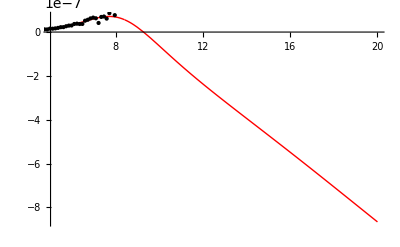

129.396

8.40051

-1730.26

1.16617

4.30327

0.223197

0.00323013

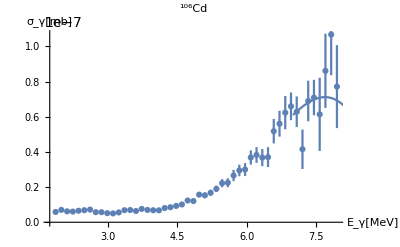

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 129.396 | 118516. | 0.0010918 | 0.999134
omega2p | 8.40051 | 3.82055 | 2.19877 | 0.0333228
Gamma1p | -1730.26 | 1.60826×10^6 | -0.00107586 | 0.999147
Gamma2p | 1.16617 | 298.193 | 0.0039108 | 0.996898
Gamma12p | 4.30327 | 297.722 | 0.014454 | 0.988535
Z10 | 0.223197 | 407.205 | 0.000548119 | 0.999565
Z20 | 0.00323013 | 0.0627758 | 0.051455 | 0.959201

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{129.396,118516.,0.0010918,0.999134},{8.40051,3.82055,2.19877,0.0333228},{-1730.26,1.60826×10^6,-0.00107586,0.999147},{1.16617,298.193,0.0039108,0.996898},{4.30327,297.722,0.014454,0.988535},{0.223197,407.205,0.000548119,0.999565},{0.00323013,0.0627758,0.051455,0.959201}}

1.36617

1.36617

```mathematica
(*TSE SMLO GDR and PDG G=const !!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[-Im[(2.1297×10^-6+(«1»«1»«5»)/(«1»))/(57.3581+«3»+(«19» «1»)/(«1»))+(«22»«1»«1»)/(«1»)]]

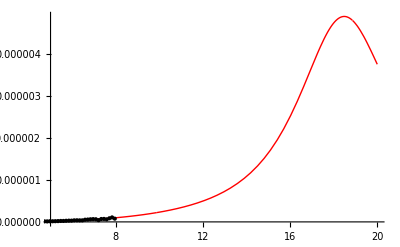

19.9949

7.57352

-2.02511

5.68261

11.7108

0.0224787

0.00145935

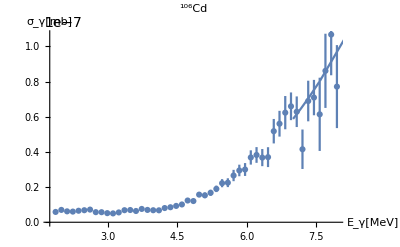

```mathematica
(*TSE SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[-Im[(2.73619×10^-7)/(48.9937-(1.-«20» ⅈ) «1»)+(«18»)/(«21»«1»«1»«1»«1»)]]

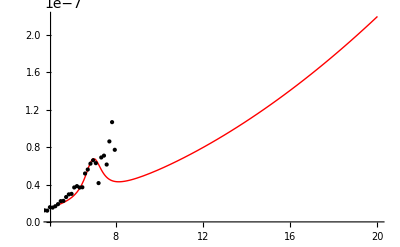

2464.89

6.99955

733.457

0.961391

261.003

0.000523086

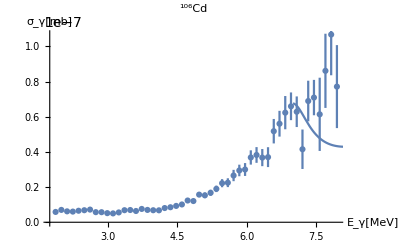

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 2464.89 | 5.64921×10^7 | 0.0000436326 | 0.999965
omega2p | 6.99955 | 0.32338 | 21.6449 | 4.35506×10^-25
Gamma1p | 733.457 | 2.54919×10^6 | 0.000287721 | 0.999772
Gamma2p | 0.961391 | 1.00676 | 0.954931 | 0.34483
Z10 | 261.003 | 1.4501×10^7 | 0.0000179989 | 0.999986
Z20 | 0.000523086 | 0.000325654 | 1.60626 | 0.11537

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{2464.89,5.64921×10^7,0.0000436326,0.999965},{6.99955,0.32338,21.6449,4.35506×10^-25},{733.457,2.54919×10^6,0.000287721,0.999772},{0.961391,1.00676,0.954931,0.34483},{261.003,1.4501×10^7,0.0000179989,0.999986},{0.000523086,0.000325654,1.60626,0.11537}}

14.5233

14.5233

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[-Im[(9.22975×10^-6)/(151.645+(0.+«1») «5»-omega^2)+(«19»)/(«19»-«1»)]]

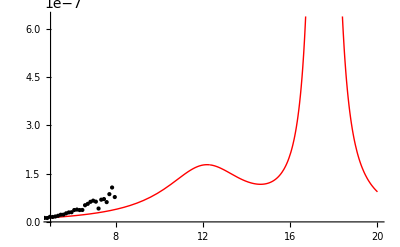

17.5331

12.3144

1.35519×10^-6

4.51324

4.75062

0.00303805

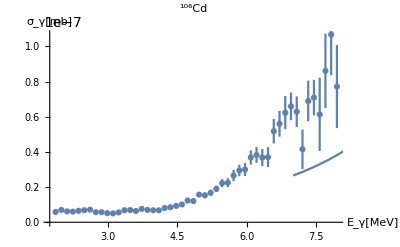

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 17.5331 | 41207.2 | 0.000425485 | 0.999662
omega2p | 12.3144 | 1196.13 | 0.0102953 | 0.991832
Gamma1p | 1.35519×10^-6 | 28.337 | 4.7824×10^-8 | 1
Gamma2p | 4.51324 | 627.59 | 0.00719139 | 0.994295
Z10 | 4.75062 | 4.96697×10^7 | 9.56443×10^-8 | 1.
Z20 | 0.00303805 | 0.792285 | 0.00383454 | 0.996958

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{17.5331,41207.2,0.000425485,0.999662},{12.3144,1196.13,0.0102953,0.991832},{1.35519×10^-6,28.337,4.7824×10^-8,1},{4.51324,627.59,0.00719139,0.994295},{4.75062,4.96697×10^7,9.56443×10^-8,1.},{0.00303805,0.792285,0.00383454,0.996958}}

12.1991

12.1991

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG G=const !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{4.68094×10^-10,4.88686×10^-10,4.35272×10^-10,4.01826×10^-10,4.8507×10^-10,4.43339×10^-10,3.94548×10^-10,3.41589×10^-10,4.08984×10^-10,3.69075×10^-10,3.34294×10^-10,4.37803×10^-10,4.28379×10^-10,5.218×10^-10,4.97133×10^-10,4.97538×10^-10,4.73024×10^-10,5.04021×10^-10,5.41605×10^-10,7.29275×10^-10,8.04627×10^-10,9.34743×10^-10,8.47702×10^-10,1.01235×10^-9,1.04849×10^-9,1.23642×10^-9,1.56393×10^-9,1.70729×10^-9,1.82082×10^-9,2.30575×10^-9,2.51248×10^-9,3.22104×10^-9,3.288×10^-9,3.66107×10^-9,4.05941×10^-9,4.46552×10^-9,4.8696×10^-9,5.64992×10^-9,6.95287×10^-9,7.32759×10^-9,9.45362×10^-9,7.87577×10^-9,8.70532×10^-9,1.12174×10^-8,1.15454×10^-8,1.00584×10^-8,2.08231×10^-8,2.1092×10^-8,2.31546×10^-8,2.35962×10^-8}

FittedModel[-Im[43616.8/(9.56097×10^6+(0.+«1») «5»-omega^2)+(«22»)/(«18»-«1»)]]

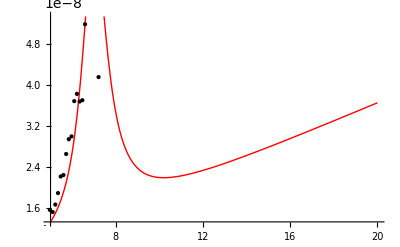

3092.08

7.07709

3.79045

1.4459

208.846

0.000747092

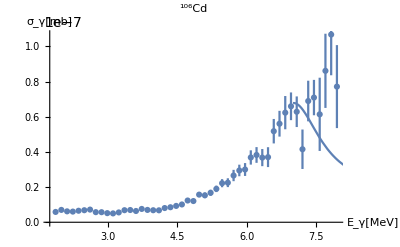

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 3092.08 | 1.39805×10^8 | 0.0000221171 | 0.999982
omega2p | 7.07709 | 0.251107 | 28.1836 | 8.51×10^-30
Gamma1p | 3.79045 | 1.71186×10^7 | 2.21424×10^-7 | 1.
Gamma2p | 1.4459 | 0.686461 | 2.10632 | 0.0409156
Z10 | 208.846 | 4.69618×10^8 | 4.44716×10^-7 | 1.
Z20 | 0.000747092 | 0.000226229 | 3.30237 | 0.00190933

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{3092.08,1.39805×10^8,0.0000221171,0.999982},{7.07709,0.251107,28.1836,8.51×10^-30},{3.79045,1.71186×10^7,2.21424×10^-7,1.},{1.4459,0.686461,2.10632,0.0409156},{208.846,4.69618×10^8,4.44716×10^-7,1.},{0.000747092,0.000226229,3.30237,0.00190933}}

6.86732

6.86732

```mathematica
(*independent Gamma12p=0, SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

```mathematica
"E:\\Sasha\\work\\Students\\Kucher\\Cd106\\FigSigmaFit106Cd.eps"
```

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

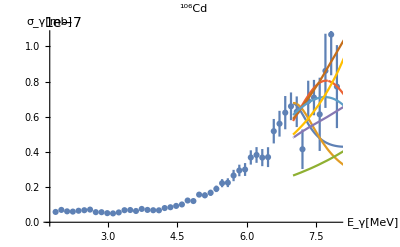

```mathematica
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[{ResponseFuncPDRsmloGDRsmlo[x],ResponseFuncPDRsmloGDRcons[x],ResponseFuncPDRconsGDRsmlo[x],ResponseFuncTSEgam0[x],ResponseFuncTSEPDRsmloGDRsmlo[x],ResponseFuncTSEPDRsmloGDRcons[x],ResponseFuncTSEPDRconsGDRsmlo[x],ResponseFuncTSEgam[x]},{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
```

```mathematica
Chi2PDRsmloGDRsmlo
Chi2PDRsmloGDRcons
Chi2PDRconsGDRsmlo
Chi2TSEgam0
Chi2TSEPDRsmloGDRsmlo
Chi2TSEPDRsmloGDRcons
Chi2TSEPDRconsGDRsmlo
Chi2TSEgam
```

14.5233

6.86732

12.1991

8.05124

12.5909

1.33486

1.36617

1.33373